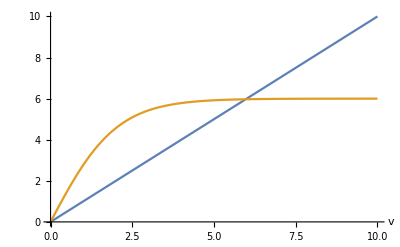

```mathematica
Λ=-12;
Plot[{v,Abs[Λ]/2 Tanh[v/2]},{v,0,10},AxesLabel->{"v",None}]
```

```mathematica
f[Λ_,p_,v_]:=v Sinh[v]+Λ Sinh[p v]Sinh[(1-p)v]
```

```mathematica
solution[λ_,P_]:=v/.FindRoot[f[λ,P,v],{v,4}]
```

```mathematica
p1[λ_]:=1/2(1-√((-4+Abs[λ])/Abs[λ]));
p2[λ_]:=1/2(1+√((-4+Abs[λ])/Abs[λ]));
```

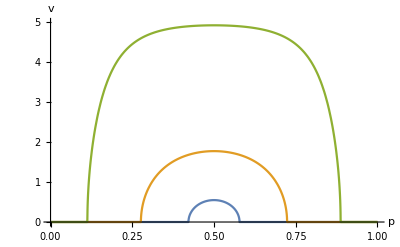

```mathematica
Plot[{solution[-4.1,P],solution[-5,P],solution[-10,P]},{P,0,1},PlotRange->{0,5},GridLines->{{p1[-4.1],p2[-4.1],p1[-5],p2[-5],p1[-10],p2[-10]},None},AxesLabel->{"p","v"}]
```

```mathematica
g[Λ_,p_,u_]:=u Sin[u]+Λ Sin[p u]Sin[(1-p)u]
```

```mathematica
solutionF[λ_]:=If[Abs[λ]>4,I solution[λ,1/2],u/.FindRoot[g[λ,1/2,u],{u,4}]]
```

```mathematica
ψ[k_,x_]:=If[x<1/2,Sin[k x],Sin[k(1-x)]]
```

```mathematica
ψ[x_]=Table[ψ[solutionF[λ],x],{λ,{0,-2,-3,-3.5,-4.5,-5,-10}}];
```

```mathematica
norm=Sqrt[Integrate[Abs[ψ[x]]^2,{x,0,1}]];
```

```mathematica
ψ[x_]=ψ[x]/norm;
```

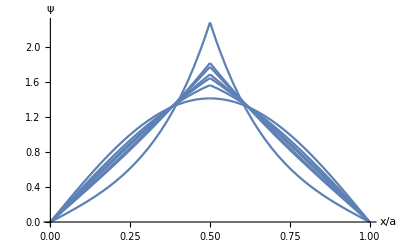

```mathematica
Plot[Abs[ψ[x]],{x,0,1},AxesLabel->{"x/a","ψ"}]
```